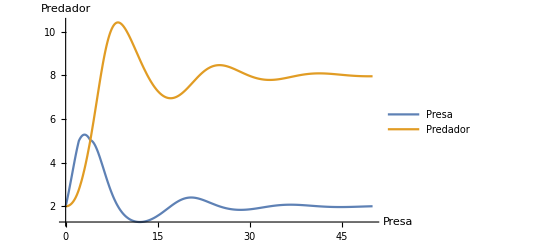

```mathematica
(* Define parameters *)
a = 1;
b = 0.1;
c = 0.2;
d = 0.1;
K = 10;
xt = 5;
yt = 5;
theta1 = 0.1;
tau = 0.1;
theta2 = 0.1;

(* Define initial conditions *)
x0 = 2;
y0 = 2;

(* Define differential equations *)
eqns = {x'[t] == a*x[t]*(1 - x[t]/K) - b*x[t]*y[t] - If[x[t] > xt && y[t] < yt, theta1*x[t], 0], 
        y'[t] == d*x[t]*y[t] - c*y[t] + If[x[t] > xt && y[t] > yt, tau, 0]};

(* Solve the differential equations *)
sol = NDSolve[{eqns, x[0] == x0, y[0] == y0}, {x, y}, {t, 0, 50}];

(* Plot the solution with labeled axis *)
Plot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 50}, 
     AxesLabel -> {"Presa", "Predador"},
     LabelStyle -> Directive[Bold, Medium],
     PlotLegends -> {"Presa", "Predador"}]
```

Ciclo Limite

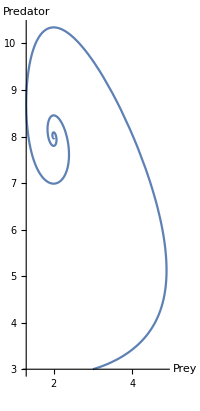

```mathematica
(* Define parameters *)
a = 1;
b = 0.1;
c = 0.2;
d = 0.1;
K = 10;
xt = 5;
yt = 5;
theta1 = 0.1;
tau = 0.1;
theta2 = 0.1;

(* Define differential equations *)
eqns = {x'[t] == a*x[t]*(1 - x[t]/K) - b*x[t]*y[t] - If[x[t] > xt && y[t] < yt, theta1*x[t], 0], 
        y'[t] == d*x[t]*y[t] - c*y[t] + If[x[t] > xt && y[t] > yt, tau, 0]};

(* Define initial conditions on the limit cycle *)
x0 = 3;
y0 = 3;

(* Solve the differential equations *)
sol = NDSolve[{eqns, x[0] == x0, y[0] == y0}, {x, y}, {t, 0, 50}];

(* Plot the limit cycle *)
ParametricPlot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 50}, 
               PlotRange -> All,
               AxesLabel -> {"Prey", "Predator"},
               LabelStyle -> Directive[Bold, Medium]]
```